# NG22P03. Метод главных компонент

КМ2021, курс 2, семестр 4
02-март-2022

### 0.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Dimensions[data=Import["NG22P03Problem.xlsx",{"Sheets","Train"}]]
```

{2494,25}

```mathematica
Dimensions[unknown=Import["NG22P03Problem.xlsx",{"Sheets","Unknown"}]]
```

{11,25}

### 1. Гистограмма

```mathematica
(*Сохраняем только данные без названий групп и т.п.*)
```

```mathematica
Dimensions[data=Drop[data,4]]
```

{2490,25}

```mathematica
Dimensions[unknown=Drop[unknown,1]]
```

{10,25}

```mathematica
(*Метки и сами данные*)
```

```mathematica
TrainLabel=data⟦;;,1⟧;
Train = data⟦;;,2;;⟧;
```

```mathematica
(*Индексы мужских параметров и женских*)
```

```mathematica
menind=Flatten[Position[TrainLabel,"М"]];
womenind=Flatten[Position[TrainLabel,"Ж"]];
```

```mathematica
(*Гистограммы первого параметра, т.е. возраста*)
```

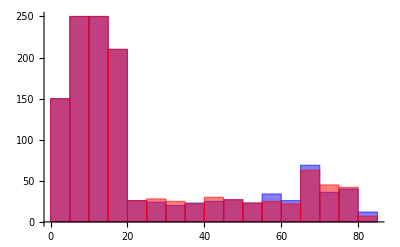

```mathematica
Histogram[{Train⟦menind,1⟧,Train⟦womenind,1⟧},ChartStyle->{Blue,Red}]
```

```mathematica
Manipulate[Histogram[{Train⟦menind,x⟧,Train⟦womenind,x⟧},ChartStyle->{Blue,Red}],{{x,1,"Параметр"},Range[24]}]
```

### 2. Стандартизация данных

```mathematica
(*Mean и StandardDeviation вычисляют по колонкам, т.е. по каждому параметру*)
```

```mathematica
μ=Mean[Train]
```

{23.7365,1475.81,1359.34,1192.17,915.927,644.727,1740.28,774.446,667.254,498.173,205.344,378.018,126.771,412.282,503.627,355.109,635.218,213.485,307.039,367.81,161.676,73.4859,222.516,85.8707}

```mathematica
σ=StandardDeviation[Train]
```

{23.0537,278.212,275.005,239.951,188.021,134.713,341.787,130.622,127.046,96.9161,41.7712,80.6091,27.5706,99.7519,113.852,68.0726,131.98,51.6971,78.4639,74.2045,30.2898,12.8686,40.2598,13.6676}

```mathematica
kmSTD[sample_List]:=(sample-μ)/σ
```

```mathematica
Dimensions[Data=kmSTD/@Train]
```

{2490,24}

```mathematica
Data//First
```

{-0.72598,-0.861952,-0.935775,-0.817531,-0.89845,-1.03722,-0.545023,-0.784291,-0.820603,-1.23997,-0.750378,-0.756962,-0.64458,-0.433892,-0.971677,-0.221952,-0.986651,-1.05393,-0.918121,-0.779063,-0.451515,-1.20339,-0.633775,-0.94169}

### 3. Правило трех сигм

```mathematica
(*Если использовать уже нормализованные данные, интервалы не нужно умножать на μ и σ*)
```

```mathematica
BinCounts[Data⟦;;,1⟧,{{-Infinity,-3,-2,-1,0,1,2,3,Infinity}}]
```

{0,0,0,1758,236,314,182,0}

```mathematica
(*Количество в процентах*)
```

```mathematica
BinCounts[Data⟦;;,1⟧,{{-Infinity,-3,-2,-1,0,1,2,3,Infinity}}]/Length[Data]//N//PercentForm
```

{0%,0%,0%,70.6%,9.478%,12.61%,7.309%,0%}

```mathematica
kmPercent[x_]:=StringJoin[ToString[#],"%"]&/@N[(100BinCounts[Data⟦;;,x⟧,{{-Infinity,-3,-2,-1,0,1,2,3,Infinity}}])/Length[Data],4]
```

```mathematica
(*Т.к. мы стандартизировали данные, у них μ равно 0 и σ равна 1, поэтому функция плотности вероятности выглядит следующим образом*)
```

```mathematica
kmPDF=PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Manipulate[
Column[{
Grid[{{"...",-3,-2,-1,1,2,3,"..."},kmPercent[ind]},Frame->All],
Show[Histogram[Data⟦;;,ind⟧,Automatic,"PDF",ChartStyle->{LightGray},ImageSize->Medium],Plot[kmPDF,{x,-4,4},Filling->Bottom]]
}],
{{ind,11,"Параметр"},Range[24]}]
```

```mathematica
(*Из значений процентов можно заметить, что наибольшее количество попадает в интервал от [-1, 1], или [μ-σ, μ+σ] для нестандиртизированных данных, затем менее на интервалах [-2, -1] и [1, 2] и самая малость на остальных интервалах*)
```

### 4. Сингулярное разложение матрицы

```mathematica
(*Сингулярное разложение матрицы можно использовать для нахождения сингулярных чисел. Затем, задав какой-то порог значений, можно отбросить некоторые из меньших сингулярных чисел, т.е. менее важных параметров. Таким образом уменьшается размерность данных и тем самым достигается экономия памяти*)
```

```mathematica
{U,S,V}=SingularValueDecomposition[Data];
```

```mathematica
ClearAll[kmMatrixPlot];
kmMatrixPlot[M_,opts___]:=MatrixPlot[
Rescale[M,{-#,#}&@Max@Abs@M],
ColorFunctionScaling->False,
ColorFunction->(If[0.4999<#<0.5001,White,ColorData["GreenPinkTones",#]]&),
opts]
```

```mathematica
(*Визуализация матриц*)
```

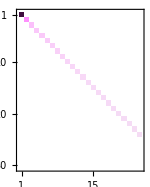
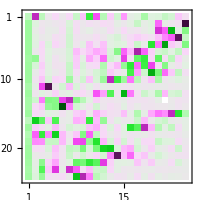
-Graphics--Graphics--Graphics-

```mathematica
{kmMatrixPlot[U,ImageSize->200],kmMatrixPlot[Take[S,30],ImageSize->150],kmMatrixPlot[V,ImageSize->200]}//Row
```

```mathematica
(*Сингулярные значения находятся по диагонали*)
```

```mathematica
singValues=Diagonal[S]
```

{221.632,60.452,31.7546,26.3442,25.4299,23.3993,21.8656,20.1363,19.21,17.2902,16.5563,15.658,14.7236,14.1885,13.8677,13.5099,13.4247,13.3358,12.6117,12.1955,12.0796,11.7015,11.3218,11.1219}

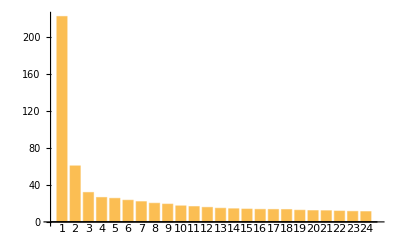

```mathematica
BarChart[singValues,ChartLabels->Range[Length[singValues]]]
```

```mathematica
Norm[U⟦;;,1;;1⟧.S⟦1;;1,1;;1⟧.V⟦;;,1;;1⟧ᵀ]
```

221.632

```mathematica
Norm[Data-U⟦;;,1;;1⟧.S⟦1;;1,1;;1⟧.V⟦;;,1;;1⟧ᵀ]
```

60.452

```mathematica
AbsoluteErr[ind_]:=Norm[Data-U⟦;;,1;;ind⟧.S⟦1;;ind,1;;ind⟧.V⟦;;,1;;ind⟧ᵀ]
```

```mathematica
(*Абсолютные и онтносительные погрешности*)
```

```mathematica
Grid[Join[{{"n","SV","Δ","δ%"}},With[{norm=Norm[Data]},Chop[{#,singValues⟦#⟧,AbsoluteErr[#],(AbsoluteErr[#]*100)/norm}]&/@Range[24]]],Frame->All]
```

n | SV | Δ | δ%
1 | 221.632 | 60.452 | 27.2759
2 | 60.452 | 31.7546 | 14.3277
3 | 31.7546 | 26.3442 | 11.8865
4 | 26.3442 | 25.4299 | 11.4739
5 | 25.4299 | 23.3993 | 10.5577
6 | 23.3993 | 21.8656 | 9.86575
7 | 21.8656 | 20.1363 | 9.08548
8 | 20.1363 | 19.21 | 8.66753
9 | 19.21 | 17.2902 | 7.8013
10 | 17.2902 | 16.5563 | 7.4702
11 | 16.5563 | 15.658 | 7.06485
12 | 15.658 | 14.7236 | 6.64328
13 | 14.7236 | 14.1885 | 6.40183
14 | 14.1885 | 13.8677 | 6.2571
15 | 13.8677 | 13.5099 | 6.09563
16 | 13.5099 | 13.4247 | 6.0572
17 | 13.4247 | 13.3358 | 6.0171
18 | 13.3358 | 12.6117 | 5.69037
19 | 12.6117 | 12.1955 | 5.50258
20 | 12.1955 | 12.0796 | 5.45028
21 | 12.0796 | 11.7015 | 5.27972
22 | 11.7015 | 11.3218 | 5.10839
23 | 11.3218 | 11.1219 | 5.0182
24 | 11.1219 | 0 | 0

### 5. Выделение главных компонент

```mathematica
toPC[sample_List,n_Integer]:=Vᵀ⟦n⟧.sample
toPC[sample_List]:=Vᵀ.sample
```

```mathematica
toPC[Data⟦1⟧]
```

{3.98974,-0.549751,0.127811,-0.162341,-0.0287173,-0.340589,0.295894,0.165761,0.0214831,-0.0497045,0.234755,-0.226046,-0.201819,0.521704,0.111359,0.0787917,-0.0915218,-0.179991,-0.113555,-0.109032,0.0143083,-0.0227332,0.154323,0.049296}

```mathematica
toPC[Data⟦1⟧,1]
```

3.98974

```mathematica
Dimensions[PC=Table[toPC[sample,n],{sample,Data},{n,1,24}]]
```

{2490,24}

```mathematica
Dimensions[PC=toPC/@Data]
```

{2490,24}

```mathematica
Dimensions[unknownPC=toPC/@unknown⟦;;,2;;⟧]
```

{10,24}

### 6. Ковариационная матрица

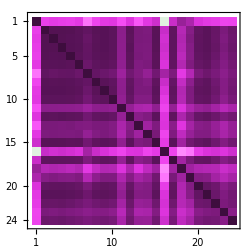
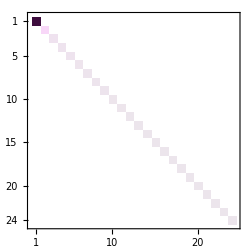

```mathematica
kmMatrixPlot[Covariance[#],ImageSize->250]&/@{Data,PC}//Row
```

```mathematica
(*Из матрицы ковариации главных компонент можно заметить, что наиболее значимой компонентой является первая (возраст). Затем, по важности идет вторая (рост) и все остальные.*)
```

### 7. Эллипс рассеивания

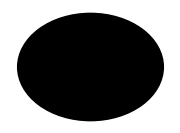

```mathematica
Graphics[Ellipsoid[{0,0},Covariance[Data⟦;;,{1,2}⟧]],ImageSize->Small]
```

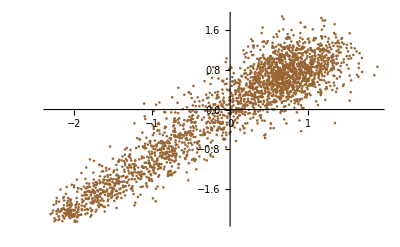

```mathematica
ListPlot[Data⟦;;,{3,6}⟧,PlotStyle->Brown]
```

```mathematica
Manipulate[
Show[
Graphics[{Brown,Opacity[0.3/#],Ellipsoid[{0,0},#^2 Covariance[Data⟦;;,{x,y}⟧]]}&/@Range[3]],
Graphics[{Blue,Opacity[0.25/#],Ellipsoid[{0,0},#^2 Covariance[PC⟦;;,{x,y}⟧]]}&/@Range[3]],
ListPlot[PC⟦;;,{x,y}⟧,PlotStyle->{Blue,Opacity[0.3]}],
ListPlot[Data⟦;;,{x,y}⟧,PlotStyle->{Brown,Opacity[0.3]}],
GridLines->Automatic,GridLinesStyle->LightGray,Frame->True,FrameStyle->Gray,PlotRange->{{-3.5,3.5},{-3.5,3.5}}
],
{{x,3,"гор"},Range[24]},{{y,6,"вер"},Range[24]}
]//Quiet
```

### 8. Эллипсоид рассеивания

```mathematica
Manipulate[
Show[
Graphics3D[{Brown,Opacity[0.3/#],Ellipsoid[{0,0,0},#^2 Covariance[Data⟦;;,{x,y,z}⟧]]}&/@Range[3]],
Graphics3D[{Blue,Opacity[0.25/#],Ellipsoid[{0,0,0},#^2 Covariance[PC⟦;;,{x,y,z}⟧]]}&/@Range[3]],
ListPointPlot3D[PC⟦;;,{x,y,z}⟧,PlotStyle->{Blue,Opacity[0.3],PointSize->Small}],
ListPointPlot3D[Data⟦;;,{x,y,z}⟧,PlotStyle->{Brown,Opacity[0.3],PointSize->Small}],
GridLines->Automatic,GridLinesStyle->LightGray,Frame->True,FrameStyle->Gray,PlotRange->{{-3.5,3.5},{-3.5,3.5},{-3.5,3.5}}
],
{{x,3,"1"},Range[24]},{{y,6,"2"},Range[24]},{{z,9,"3"},Range[24]}
]//Quiet
```

### 9. Наивный байесовский классификатор

```mathematica
μMale=Mean[Data⟦menind⟧];
μFemale=Mean[Data⟦womenind⟧];
```

```mathematica
(*Вычисляем веса согласно формуле*)
```

```mathematica
{W,W0}=With[{C=Inverse[Covariance[Data]]},{C.(μFemale-μMale),1/2(μMale.C.μMale-μFemale.C.μFemale)//Chop}]
```

{{-0.139054,-0.0301717,0.25611,-0.21394,-0.148016,0.783398,0.585628,0.178499,-0.0885678,-0.556335,-0.199149,-0.175565,0.371937,0.0222156,1.20806,0.169672,-0.163119,0.257653,1.3189,-0.634522,-0.336711,-1.40242,-0.546067,-0.661995},0}

```mathematica
(*Первый слой, берем функцию стандартизации данных kmSTD*)
```

```mathematica
layer1=kmSTD;
```

```mathematica
layer1[unknown⟦1,2;;⟧]
```

{0.835589,0.737549,0.464198,0.570252,0.846038,0.298952,0.42049,0.838711,1.00551,0.761757,0.805719,0.744108,0.479804,0.658819,1.21538,-1.07398,0.490847,0.18405,1.0828,0.0834175,0.505902,0.0399465,0.38461,0.667951}

```mathematica
(*Второй слой*)
```

```mathematica
layer2=UnitStep[W.# + W0]&;
```

```mathematica
layer2[layer1[unknown⟦2,2;;⟧]]
```

1

```mathematica
(*Классификатор для всех главных компонент*)
```

```mathematica
NBC[x_]:=layer2[layer1[x]];
```

```mathematica
testfriend=Flatten[Position[unknown⟦;;,1⟧,"Ж"]];
testfoe=Flatten[Position[unknown⟦;;,1⟧,"М"]];
```

```mathematica
(*Результаты классификации на unknown, 1-женщина, 0 - мужчина*)
```

```mathematica
NBC/@unknown⟦;;,2;;⟧
```

{1,1,1,0,0,1,1,0,0,1}

```mathematica
(*Ошибка первого рода*)
```

```mathematica
pred=NBC/@unknown⟦testfriend,2;;⟧;
Count[pred,0]/Length[pred]//N//PercentForm
```

20%

```mathematica
(*Ошибка второго рода*)
```

```mathematica
pred=NBC/@unknown⟦testfoe,2;;⟧;
Count[pred,1]/Length[pred]//N//PercentForm
```

40%

```mathematica
(*Результаты классификации на исходных данных и ошибки первого и второго рода*)
```

```mathematica
pred=NBC/@data⟦womenind,2;;⟧;
Count[pred,0]/Length[pred]//N//PercentForm
```

17.91%

```mathematica
pred=NBC/@data⟦menind,2;;⟧;
Count[pred,1]/Length[pred]//N//PercentForm
```

19.28%

#### Для разного количества главных компонент

```mathematica
(*Вычисление весов*)
```

```mathematica
NBCWeights[n_]:=Quiet@Module[
{Data,C,μMale,μFemale},
Data=U⟦;;,1;;n⟧.S⟦1;;n,1;;n⟧.V⟦;;,1;;n⟧ᵀ;
C=Inverse[Covariance[Data]];
μMale=Mean[Data⟦menind⟧];
μFemale=Mean[Data⟦womenind⟧];
{C.(μFemale-μMale),1/2(μMale.C.μMale-μFemale.C.μFemale)//Chop}
]
```

```mathematica
{W,W0}=NBCWeights[1]
```

{{-1.,-0.5,0.25,0.,0.25,-0.125,-0.5,0.,0.28125,-0.375,0.390625,1.,0.09375,-0.5,-1.25,0.40625,0.,0.5,0.3125,-0.1875,0.1875,0.125,0.125,-0.75},-0.0276458}

```mathematica
NBCErr[n_]:=Module[
{pred,res={n}},
{W,W0}=NBCWeights[n];
pred=NBC/@data⟦womenind,2;;⟧;
AppendTo[res,100 Count[pred,0]/Length[pred]//N];
pred=NBC/@data⟦menind,2;;⟧;
AppendTo[res,100Count[pred,1]/Length[pred]//N];
Return[res]
]
```

```mathematica
NBCErr[1]
```

{1,45.6225,52.2088}

```mathematica
Grid[Join[{{"Главных компонент","Женщину за мужчину","Мужчину за женщину"}},NBCErr/@{1,2,3,5,11,24}],Frame->All]
```

Главных компонент | Женщину за мужчину | Мужчину за женщину
1 | 45.6225 | 52.2088
2 | 51.3253 | 56.2249
3 | 42.7309 | 37.9116
5 | 41.5261 | 40.8032
11 | 34.7791 | 39.1165
24 | 17.9116 | 19.2771